```mathematica
Subscript[P, 1]=10^4;
Subscript[P, 2]=5×10^3;
Subscript[f, 1]=1.5×10^-4;
Subscript[f, 2]=√2×10^-4;
Subscript[f, 3]=3×10^-4;
Subscript[eq, 1]=-Subscript[P, 1]+(k Subscript[f, 1])/(2 √2 L) (x+y)+(k Subscript[f, 3])/(2 √2 L) (x-y);
Subscript[eq, 2]=-Subscript[P, 2]+(k Subscript[f, 1])/(2 √2 L) (x+y)+(k Subscript[f, 2])/L y+(k Subscript[f, 3])/(2 √2 L) (y-x);
Solve[{Subscript[eq, 1]==0,Subscript[eq, 2]==0},{x,y}]
```

{{x→(7.26749×10^7 L)/k,y→(2.94628×10^7 L)/k}}

```mathematica
u=(7.267486362195073*^7 L)/k;
v=(2.946278254943946*^7 L)/k;
Subscript[N, 1]=(k Subscript[f, 1])/(√2 L) (u+v) (√2)/2
Subscript[N, 2]=k Subscript[f, 2]/L v
Subscript[N, 3]=((√2)/2 (-u+v))/(√2 L) k Subscript[f, 3]
```

7660.32

4166.67

-6481.81

```mathematica
eqq=n^2 (√2  L)/(2 k Subscript[f, 1])+((Subscript[P, 1]+Subscript[P, 2]-√2 n)^2 L)/(2 k Subscript[f, 2])+((n-√2  Subscript[P, 1])^2 √2 L)/(2 k Subscript[f, 3]);
Solve[D[eqq,n]==0,n]
```

{{n→7660.32}}

```mathematica
Subscript[P, 1]+Subscript[P, 2]-√2  7660.32
7660.32-√2  Subscript[P, 1]
```

4166.67

-6481.82

```mathematica
∫_0^α Sin[θ] Cos[θ] ⅆθ//TraditionalForm
```

(sin^2(α))/2

```mathematica
∫_0^α Sin[θ] Cos[α-θ] ⅆθ//TraditionalForm
```

1/2 α sin(α)

```mathematica
∫_0^π 1/2  α Sin[α] ⅆα//TraditionalForm
```

π/2

```mathematica
∫_0^π (Cos[α]-1)^2 ⅆα
```

(3 π)/2

```mathematica
∫_0^π (Cos[α]-1-1/2 α Sin[α]) (Cos[α]-1) ⅆα
```

(17 π)/8

```mathematica
∫_0^π (Cos[α]-1)×(Cos[α]-1+1/2 α Sin[α]) ⅆα
```

(7 π)/8

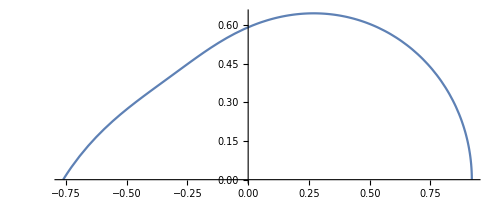

```mathematica
M=(P R)/(2 π)  (-1+1/2 Cos[α]-α Sin[α]);
M=(M+1)/.P->1/.R->1;
PolarPlot[M,{α,0,π}]
```